# Deflection of Charged Particle in Magnetic field

## Generate Magnetic field

```mathematica
(* magnetic field of Single coil *)
(* a = radius of coil *)
(* z = z position, assume center on {x,y}={0,0} *)
(* {ρ,ζ} = observe position *)
BρSC[a_,z_,ρ_,ζ_]:=(z-ζ)/(ρ √((z-ζ)^2+(a+ρ)^2))(EllipticK[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)]- (a^2+ρ^2+(ζ-z)^2)/((a-ρ)^2+(ζ-z)^2) EllipticE[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)])
BζSC[a_,z_,ρ_,ζ_]:=If[ρ>0,1/(√((ζ-z)^2+(a+ρ)^2))( EllipticK[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)]+(a^2-ρ^2-(ζ-z)^2)/((a-ρ)^2+(ζ-z)^2) EllipticE[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)] ),(a^2 π)/((a^2+(z-ζ)^2)^(3/2))]
```

```mathematica
DisplayfieldM[a_,z_,n_,d_,streampoints_,range_]:=
StreamDensityPlot[
Sum[{ BρSC[a,z+(m -(n-1)/2)d,R,Z],BζSC[a,z+(m -(n-1)/2)d,Abs[R],Z]},{m,0,n-1,1}]
,{R,Min[range[[1]]],Max[range[[1]]]},{Z,Min[range[[2]]],Max[range[[2]]]},StreamPoints->streampoints, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->800,AspectRatio->(Max[range[[2]]]-Min[range[[2]]])/(Max[range[[1]]]-Min[range[[1]]])]
```

```mathematica
DisplayfieldM[1,0, 10,0.1,50,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

```mathematica
FieldonXYplane[a_,z_,n_,d_,ρ_]:=Sum[{ BρSC[a,z+(m -(n-1)/2)d,ρ,0],BζSC[a,z+(m -(n-1)/2)d,Abs[ρ],0]},{m,0,n-1,1}]
```

```mathematica
(* The field strength on XY plane *)
Manipulate[Plot[FieldonXYplane[a,0,10,d,Abs[ρ]][[2]],{ρ,-10a,10a},PlotRange->All, Frame->True, FrameLabel-> {"radius","field strenght"},
GridLines->Automatic],
{a,0.11,2},{{d,2},0.1,2}]
```

## Calculate the deflection

```mathematica
μ0=4π 10^-7; (* H m^-1 *)
e =  1.602176487 10^-19; (* C *)
mp=1.672621637 10^-27; (* kg *)
mpR=mp c^2/(e 10^6); (* MeV *)
c=299792458;
```

### Discrete Time method

```mathematica
B[ρ_,current_]:=If[ρ<1,1,0]
```

```mathematica
Field0=Limit[FieldonXYplane[0.5,0,10,0.3,g],g->0][[2]];
B[ρ_,current_]:=current (FieldonXYplane[0.5,0,10,0.3,Abs[ρ]][[2]])/Field0
Manipulate[Plot[B[ρ,current],{ρ,-1.5,1.5},PlotRange->All],{{current,1},1,2}]
```

Travel Length = | 5.99585 | Total Time | 5.×10^-8 |  | 
β | 0.4 | K.E. | 85.4667 | Step length = | 0.00599585
center B-field | 7. |  |  |  | 
init. accl. | -1.03698×10^15 |  |  |  | 
initial radius | -13.8673 |  |  |  |

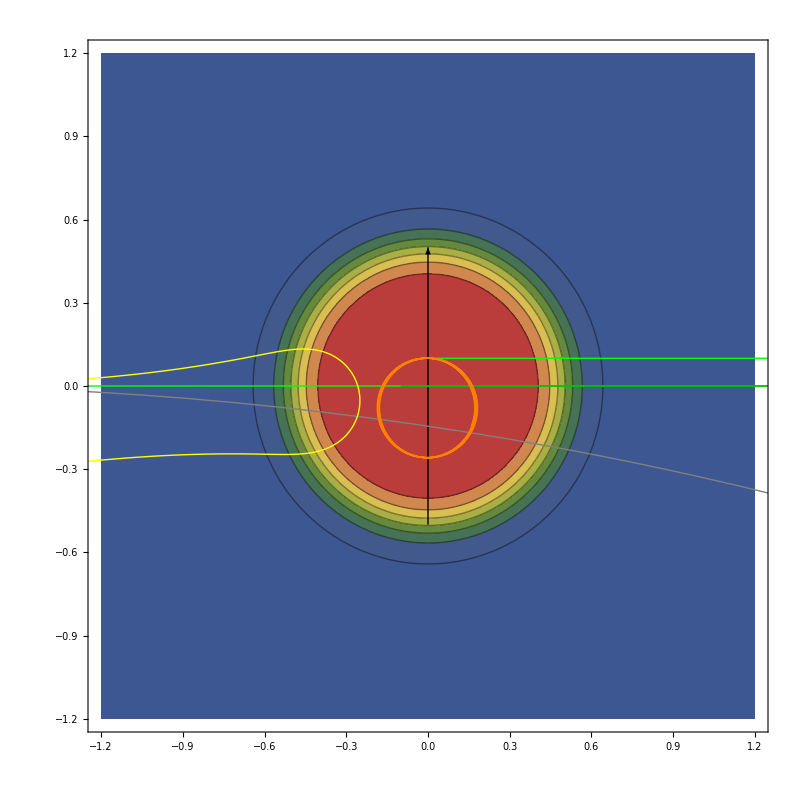

```mathematica
θout=0°;
Remove[v,r,v1,v2,r1,r2,p,p1,p2];
speed=0.4c;
β=speed/c;
p0=mp speed 1/(√(1-(β)^2)){Cos[θout],Sin[θout]};
r10={-2,0};(* m*)
r20={0,0.1};
Δt=0.5 10^-10; (* s*)
p1[1,1]=p0[[1]];
p1[1,2]=p0[[2]];
r1[1,1]=r10[[1]];
r1[1,2]=r10[[2]];
p2[1,1]=p0[[1]];
p2[1,2]=p0[[2]];
r2[1,1]=r20[[1]];
r2[1,2]=r20[[2]];
numArray=1000;
range={{-1.2,1.2},{-1.2,1.2}};
field=7;
TableForm[{
{"Travel Length =",Δt speed  numArray//N,"Total Time", Δt numArray//N},
{"β",β//N,"K.E.",(1/(√(1-β^2))-1)mp c^2/(e 10^6), "Step length =",Δt speed//N },
{"center B-field" , field//N},
{"init. accl.",e/mp speed   B[Norm[{r1[1,1],r1[1,2]}],field]//N},
{"initial radius",(mp speed)/(B[Norm[{r1[1,1],r1[1,2]}],field]e)//N}}
]
Monitor[Table[
p1[i+1,1]=e/mp p1[i,2] B[Norm[{r1[i,1],r1[i,2]}],field]Δt+p1[i,1];
p1[i+1,2]=-e/mp p1[i,1]B[Norm[{r1[i,1],r1[i,2]}],field]Δt+p1[i,2];
{p1[i+1,1],p1[i+1,2]}=Norm[p0]Normalize[{p1[i+1,1],p1[i+1,2]}];
v1[i]=Normalize[{p1[i,1],p1[i,2]}] (Norm[{p1[i,1],p1[i,2]}]c)/(√(mp^2 c^2+Norm[{p1[i,1],p1[i,2]}]^2));
r1[i+1,1]=v1[i][[1]]Δt+r1[i,1];
r1[i+1,2]=v1[i][[2]]Δt+r1[i,2];
p2[i+1,1]=e/mp p2[i,2] B[Norm[{r2[i,1],r2[i,2]}],field]Δt+p2[i,1];
p2[i+1,2]=-e/mp p2[i,1]B[Norm[{r2[i,1],r2[i,2]}],field]Δt+p2[i,2];
{p2[i+1,1],p2[i+1,2]}=Norm[p0]Normalize[{p2[i+1,1],p2[i+1,2]}];
v2[i]=Normalize[{p2[i,1],p2[i,2]}] (Norm[{p2[i,1],p2[i,2]}]c)/(√(mp^2 c^2+Norm[{p2[i,1],p2[i,2]}]^2));
r2[i+1,1]=v2[i][[1]]Δt+r2[i,1];
r2[i+1,2]=v2[i][[2]]Δt+r2[i,2];
,{i,1,numArray}];,i]
Show[
ContourPlot[B[Norm[{x,y}],field],{x,Min[range[[1]]],Max[range[[1]]]},{y,Min[range[[2]]],Max[range[[2]]]},PlotPoints->30,ColorFunction->"DarkRainbow",PlotRange->All, ColorFunctionScaling->True],
Graphics[{
Black,Arrow[{{-0.1,0},{1.5,0}}],
Arrow[{{0,-0.5},{0,0.5}}],
Green, Line[{r10,r10+v1[1] Δt numArray}], Line[{r20,r20+v2[1] Δt numArray}],
Gray,Circle[{r1[1,1],r1[1,2]}+Abs[(mp speed)/(B[Norm[{r1[1,1],r1[1,2]}],field]e)]{Cos[θout-90°],Sin[θout-90°]},Abs[(mp speed)/(B[Norm[{r1[1,1],r1[1,2]}],field]e)]]
}],
ListPlot[{
Table[{r1[i,1],r1[i,2]},{i,1,numArray}],
Table[{r2[i,1],r2[i,2]},{i,1,numArray}]
},Joined->True,PlotStyle->{Yellow,Orange}]
,PlotRange->range,AspectRatio->(Max[range[[2]]]-Min[range[[2]]])/(Max[range[[1]]]-Min[range[[1]]]),ImageSize->800]
```

## PP scatering

```mathematica
T1[T_,α_]:=T Cos[α/2]^2
T2[T_,α_]:=T Sin[α/2]^2
θ1[m_,T_,α_]:=ArcTan[√(T (2 m+T)) Cos[α/2]^2,(√(m T) Sin[α])/(√2)]
θ2[m_,T_,α_]:=ArcTan[√(T (2 m+T)) Sin[α/2]^2,-(√(m T) Sin[α])/(√2)]
T2β[T_,m_,A_]:=√(1-m^2/(m+A T)^2)
```

```mathematica
B[ρ_,current_]:=μ0 current/(2π) FieldonXYplane[0.11,0,10,0.1,ρ][[2]]
Manipulate[Plot[B[ρ,current],{ρ,0,1.5},PlotRange->All],{{current,5000},5000,20000}]
```

Travel Length = | 0.298131 | Total Time | 4.×10^-9 |  | 
β | 0.248614 | θ1 | 68.7755 | Step length = | 0.000149065
center B-field | 0.0609442 |  |  |  | 
init. accl. | 1.49839×10^6 |  |  |  | 
initial radius | 4.25873×10^-8 |  |  |  |

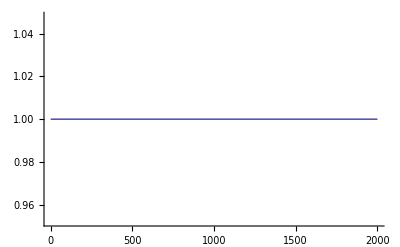

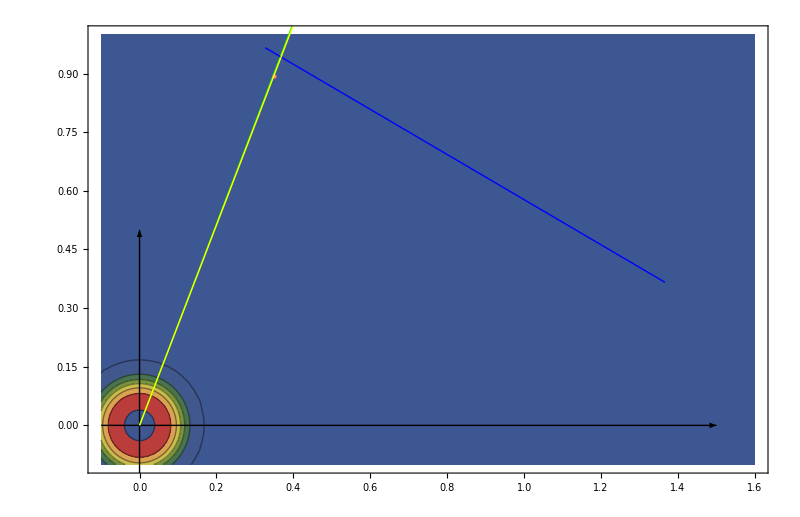

```mathematica
θNN=140°;
ET=260;
β=T2β[ET Cos[θNN/2]^2,mp c^2/(e 10^6),1];
p0=mp c^2/(e 10^6) β c 1/(√(1-(β)^2)){Cos[θ1[mp c^2/(e 10^6),ET,θNN]],Sin[θ1[mp c^2/(e 10^6),ET,θNN]]};
r0={0.000001,0};(* m*)
Δt=2 10^-12; (* s*)
p[1,1]=p0[[1]];
p[1,2]=p0[[2]];
r[1,1]=r0[[1]];
r[1,2]=r0[[2]];
numArray=2000;
range={{-0.1,1.6},{-0.1,1}};
field=5000;
TableForm[{
{"Travel Length =",Δt β c  numArray//N,"Total Time", Δt numArray//N},
{"β",β//N,"θ1",θ1[mp c^2/(e 10^6),260,θNN] 180/π//N, "Step length =",Δt β c//N },
{"center B-field" , B[Norm[{r[1,1],r[1,2]}],field]//N},
{"init. accl.",e/mp β/(√(1-β^2))  B[Norm[{r[1,1],r[1,2]}],field]//N},
{"initial radius",(mp β)/(B[Norm[{r[1,1],r[1,2]}],field]e)//N}}
]
Monitor[Table[
p[i+1,1]=e/mp p[i,2] B[Norm[{r[i,1],r[i,2]}],field]Δt+p[i,1];
p[i+1,2]=-e/mp p[i,1]B[Norm[{r[i,1],r[i,2]}],field]Δt+p[i,2];
{p[i+1,1],p[i+1,2]}=Norm[p0]Normalize[{p[i+1,1],p[i+1,2]}];
v[i]=Normalize[{p[i,1],p[i,2]}] (Norm[{p[i,1],p[i,2]}]c)/(√(mp^2 c^2+Norm[{p[i,1],p[i,2]}]^2));
r[i+1,1]=v[i][[1]]Δt+r[i,1];
r[i+1,2]=v[i][[2]]Δt+r[i,2];,{i,1,numArray}];,i]
ListPlot[Table[Norm[v[i]]/Norm[v[1]],{i,1,numArray}],Joined->True]
Show[
ContourPlot[B[Norm[{x,y}],field],{x,Min[range[[1]]],Max[range[[1]]]},{y,Min[range[[2]]],Max[range[[2]]]},PlotPoints->30,ColorFunction->"DarkRainbow",PlotRange->All, ColorFunctionScaling->True],
Graphics[{
Black,Arrow[{{-0.1,0},{1.5,0}}],
Arrow[{{0,-0.5},{0,0.5}}],
Green, Line[{r0,r0+v[1]Δt numArray}],
Blue,Line[{{1/2,(√3)/2}+{(-√3)/2,1/2}0.2,{1/2,(√3)/2}-{(-√3)/2,1/2}}],
Line[{{1/2,-(√3)/2}+{(-√3)/2,-1/2}0.2,{1/2,-(√3)/2}-{(-√3)/2,-1/2}}],
PointSize[Large],Pink,Point[{r[Round[0.8 numArray],1],r[Round[0.8 numArray],2]}]
}],
ListPlot[Table[{r[i,1],r[i,2]},{i,1,numArray}],Joined->True,PlotStyle->Yellow]
,PlotRange->range,AspectRatio->(Max[range[[2]]]-Min[range[[2]]])/(Max[range[[1]]]-Min[range[[1]]]),ImageSize->800]
```

```mathematica
Y=Table[r[i,2],{i,Round[numArray 0.8],numArray}];
X=Table[{r[i,1],1},{i,Round[numArray 0.8],numArray}];
deflectedvector=Normalize[{1,LinearModelFit[{X,Y},{a,b}]["BestFitParameters"][[1]]}];
LinearModelFit[{X,Y},{a,b}][{"ParameterTable","ANOVATable"}]
(* point on 90% *)
point90={r[Round[numArray 0.9],1],r[Round[numArray 0.9],2]};
(* point on MWDC when no field *)
pointonMWDC=Normalize[v[1]](k/.Solve[{1/2,(√3)/2}==Normalize[v[1]]k-{(-√3)/2,1/2}s,{k,s}][[1]])
pointonMWDCdeflected=point90+deflectedvector(k/.Solve[pointonMWDC-point90==deflectedvector k-{(-√3)/2,1/2}s,{k,s}][[1]])
(s/.Solve[pointonMWDC-point90==deflectedvector k-{(-√3)/2,1/2}s,{k,s}][[1]])
ArcCos[Normalize[v[1]].deflectedvector] 180/π
ArcCos[Normalize[pointonMWDC].Normalize[pointonMWDCdeflected]] 180/π
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 2.56035 | 4.31985×10^-7 | 5.92694×10^6 | 1.36737796992×10^-2185
b | 0.000142138 | 1.6985×10^-7 | 836.845 | 2.04461199964×10^-649, | DF | SS | MS | F-Statistic | P-Value
b | 1 | 1.67607 | 1.67607 | 3.51286×10^13 | 1.36707628817×10^-2185
Error | 399 | 1.90372×10^-11 | 4.77124×10^-14 |  | 
Total | 400 | 1.67607 |  |  | }

{0.366312,0.94321}

{0.367963,0.942257}

-0.00190671

0.109658

0.106734